```mathematica
Manipulate[
Module[{x,y,δ,c,δc,c1,c2,f,g},
x=1;y=0.4*x;δ=0.25/5;

c[1]={{0,y/2},{0.75*x,0.35*y},{0.75*x,0.75*y},{0.75*x,y}};
δc[1]={{0,δ},{-δ,δ},{-δ,δ},{-δ,0}};
c[2]={{0,y/2},{0.25*x,y/2},{0.25*x,0}};
δc[2]={{0,δ},{δ,δ},{δ,0}};

c1[i_]:=c[i]+δc[i];c2[i_]:=c[i]-δc[i];

f[data_,i_]:=Quiet@Interpolation[BezierFunction[data[i]][#]&/@Range[0,1,0.01]];
g[data_,i_]:={#,f[data,i][#]}&/@Range[data[i][[1,1]],data[i][[-1,1]],0.01];

Graphics[{
{Thick,Red,BezierCurve@c1[#],BezierCurve@c2[#]}&/@{1,2},
{Thick,Dashed,Line@g[c1,1],Line@g[c2,1],Blue,Line@g[c1,2],Line@g[c2,2]},
FaceForm@Opacity[0.5,Red],
}]
],
Control[{{q,0.2,"feed quality"},0,1,0.1,Appearance->"Labeled"}]
]
```

```mathematica
Manipulate[
Module[{x,y,δ,V,L},
x=1;y=0.4*x;δ=0.25/5;

V=Module[{c0,δc,c1,c2,f,g,h1,h2},
c0={{0,y/2},{0.42*x,y/2},{0.75*x,0.4*y},{0.75*x,0.75*y},{0.75*x,y}};
δc={{0,δ},{-δ,δ},{-δ,δ},{-δ,δ},{-δ,0}};
c1=c0+δc;c2=c0-δc;

f[c_]:=Quiet@Interpolation[BezierFunction[c][#]&/@Range[0,1,0.01]];
g[c_]:={#,f[c][#]}&/@Range[0,c[[-1,1]],0.01];
h1=Join[{c2[[1]]},g@c1];h2=Join[g@c2,{c1[[-1]]}];

Graphics[{
{White,Polygon@Join[h1,h2]},
Thick,Line@g[c1],Line@g[c2],
Green,Point@RandomPoint[Polygon@Join[h1,h2],Round[q*500]]
}]];

L=Module[{c0,δc,c1,c2,f,g,h1,h2},
c0={{0,y/2},{0.25*x,y/2},{0.25*x,0}};
δc={{0,δ},{δ,δ},{δ,0}};
c1=c0+δc;c2=c0-δc;

f[c_]:=Quiet@Interpolation[BezierFunction[c][#]&/@Range[0,1,0.01]];
g[c_]:={#,f[c][#]}&/@Range[0,c[[-1,1]],0.01];
h1=Join[{c2[[1]]},g@c1];h2=Join[g@c2,{c1[[-1]]}];

Graphics[{
{White,Polygon@Join[h1,h2]},
Thick,Line@g[c1],Line@g[c2],
Blue,Point@RandomPoint[Polygon@Join[h1,h2],Round[q*500]]
}]];

Show[L,V]
],
Control[{{q,0.2,"feed quality"},0,1,0.1,Appearance->"Labeled"}]
]
```

```mathematica
Manipulate[
Module[{x,y,δ,c,δc,cA1,cA2,cB1,cB2,f1,g1,h1,f2,g2,h2,j},
x=1;y=0.4*x;δ=0.25/5;

c[1]={{0,y/2},{0.42*x,y/2},{0.75*x,0.4*y},{0.75*x,0.75*y},{0.75*x,y}};
δc[1]={{0,δ},{-δ,δ},{-δ,δ},{-δ,δ},{-δ,0}};
c[2]={{0,y/2},{0.25*x,y/2},{0.25*x,0}};
δc[2]={{0,δ},{δ,δ},{δ,0}};

cA1=c[1]+δc[1];cB1=c[1]-δc[1];
cA2=c[2]+δc[2];cB2=c[2]-δc[2];

(*f1[i_]:=Quiet@Interpolation[BezierFunction[c1[i]][#]&/@Range[0,1,0.01]];
g1[i_]:={#,f1[i][#]}&/@Range[0,c1[i][[-1,1]],0.01];
h1[i_]:=Join[{c2[i][[1]]},g1[i]];

f2[i_]:=Quiet@Interpolation[BezierFunction[c2[i]][#]&/@Range[0,1,0.01]];
g2[i_]:={#,f2[i][#]}&/@Range[0,c2[i][[-1,1]],0.01];
h2[i_]:=Join[g2[i],{c1[i][[-1]]}];*)

Graphics[{Thick,
{(*Point@RandomPoint[Polygon[Join[h2[1],h1[1]]],Round[(1-q)*500]],*)BezierCurve@cA1,BezierCurve@cB1},
{Red,(*Point@RandomPoint[Polygon[Join[h2[2],h1[2]]],Round[q*500]],*)BezierCurve@cA2,BezierCurve@cB2},
}]
],
Control[{{q,0.2,"feed quality"},0,1,0.1,Appearance->"Labeled"}]
]
```

```mathematica
Manipulate[
Module[{x,y,δ,c,δc,c1,c2,f1,g1,h1,f2,g2,h2,j},
x=1;y=0.4*x;δ=0.25/5;

c[1]={{0,y/2},{0.42*x,y/2},{0.75*x,0.4*y},{0.75*x,0.75*y},{0.75*x,y}};
δc[1]={{0,δ},{-δ,δ},{-δ,δ},{-δ,δ},{-δ,0}};
c[2]={{0,y/2},{0.25*x,y/2},{0.25*x,0}};
δc[2]={{0,δ},{δ,δ},{δ,0}};

c1[i_]:=c[i]+δc[i];c2[i_]:=c[i]-δc[i];

f1[i_]:=Quiet@Interpolation[BezierFunction[c1[i]][#]&/@Range[0,1,0.01]];
g1[i_]:={#,f1[i][#]}&/@Range[0,c1[i][[-1,1]],0.01];
h1[i_]:=Join[{c2[i][[1]]},g1[i]];

f2[i_]:=Quiet@Interpolation[BezierFunction[c2[i]][#]&/@Range[0,1,0.01]];
g2[i_]:={#,f2[i][#]}&/@Range[0,c2[i][[-1,1]],0.01];
h2[i_]:=Join[g2[i],{c1[i][[-1]]}];

(*j=2;*)
(*Graphics[{Thick,
{Point@RandomPoint[Polygon[Join[h2[1],h1[1]]],Round[(1-q)*500]],
BezierCurve@c1[1],BezierCurve@c2[1]
(*BezierCurve[c1[1]+{{0,0},{0,0},{-#*x,#*y},{-#*x,#*y},{-#*x,#*y}}&@0.015],Red,BezierCurve[c2[1]+{{0,0},{0,0},{-#*x,#*y},{-#*x,#*y},{-#*x,#*y}}&@0.015]*)},
{Point@RandomPoint[Polygon[Join[h2[2],h1[2]]],Round[q*500]],
(*BezierCurve@c1[2],BezierCurve@c2[2]*)},
}]*)

Graphics[{Thick,
(*{(*Point@RandomPoint[Polygon[Join[h2[1],h1[1]]],Round[(1-q)*500]],*)BezierCurve@c1[1],BezierCurve@c2[1]},
{Point@RandomPoint[Polygon[Join[h2[2],h1[2]]],Round[q*500]],BezierCurve@c1[2],BezierCurve@c2[2]},*)
{FaceForm@Opacity[0.5,Red],Polygon@Join[h1[1],h2[1]],Polygon@Join[h1[2],h2[2]]},
{Thick,Line@h1[#],Line@h2[#]}&/@{1,2},
Point@RandomPoint[Polygon@Join[h1[1],h2[1]],Round[q*500]]
}]
],
Control[{{q,0.2,"feed quality"},0,1,0.1,Appearance->"Labeled"}]
]
```

```mathematica
Manipulate[
Module[{x,y,δ,c,δc,c1,c2,f1,g1,h1,f2,g2,h2},
x=1;y=0.4*x;δ=0.25/5;

c={{0,y/2},{0.42*x,y/2},{0.75*x,0.35*y},{0.75*x,0.75*y},{0.75*x,y}};
δc={{0,δ},{-δ,δ},{-δ,δ},{-δ,δ},{-δ,0}};
c1=c+δc;c2=c-δc;

f1=Quiet@Interpolation[BezierFunction[c1][#]&/@Range[0,1,0.01]];
g1={#,f1[#]}&/@Range[0,c1[[-1,1]],0.01];
h1=Join[{c2[[1]]},g1];

f2=Quiet@Interpolation[BezierFunction[c2][#]&/@Range[0,1,0.01]];
g2={#,f2[#]}&/@Range[0,c2[[-1,1]],0.01];
h2=Join[g2,{c1[[-1]]}];

Graphics[{Thick,
{BezierCurve@c,Dashed,Blue,BezierCurve@c1,Red,BezierCurve@c2},
EdgeForm@None,FaceForm@Opacity[0.5,Red],Polygon[Join[h2,h1]]
}]
],
Control[{{q,0,"feed quality"},0,1,0.1,Appearance->"Labeled"}]
]
```

```mathematica
Manipulate[
Module[{x,y,δ,c,δc,c1,c2,f1,f2,g1,g2,h1,h2},
x=1;y=0.4*x;δ=0.25/5;

c={{0,y/2},{0.25*x,y/2},{0.25*x,0}};
δc={{0,δ},{δ,δ},{δ,0}};
c1=c+δc;c2=c-δc;

f1=Quiet@Interpolation[BezierFunction[c1][#]&/@Range[0,1,0.01]];
g1={#,f1[#]}&/@Range[0,c1[[-1,1]],0.01];
h1=Join[{c2[[1]]},g1];

f2=Quiet@Interpolation[BezierFunction[c2][#]&/@Range[0,1,0.01]];
g2={#,f2[#]}&/@Range[0,c2[[-1,1]],0.01];
h2=Join[g2,{c1[[-1]]}];

Graphics@{Thick,
{BezierCurve@c,Dashed,Blue,BezierCurve@c1,Red,BezierCurve@c2},
EdgeForm@None,FaceForm@Opacity[0.5,Red],Polygon[Join[h2,h1]]
(*Point@RandomPoint[Polygon[Join[h2,h1]],500]*)}
],
Control[{{q,0,"feed quality"},0,1,0.1,Appearance->"Labeled"}]
]
```

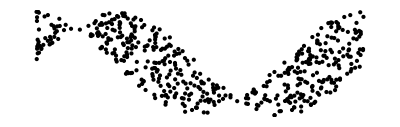

```mathematica
Quiet@Graphics@Point[RandomPoint[ImplicitRegion[Cos[x]≤y≤Sin[x]||Sin[x]≤y≤Cos[x],{{x,0,2 π},{y,-1,1}}],500]]
```

```mathematica
Module[{c1,c2,gk},
c1={{2,1},{2,0},{0,0}};
c2={{0,0.25},{1.75,0.25},{1.75,1}};

gk=JoinedCurve[{Line[{{0,0},{0,0.25}}],BezierCurve@c2,Line[{{1.75,1},{2,1}}],BezierCurve@c1}];

Graphics[{
FilledCurve[{BezierCurve@c1,Line[{{0,0},{0,0.25}}],BezierCurve@c2,Line[{{1.75,1},{2,1}}]}],
Red,Point@RandomPoint[Disk[{1,0.45},{1.3,0.9}],5000],
Blue,Point@RandomPoint[gk,500]
}]
]
```

RandomPoint::creg: The first argument JoinedCurve[{Line[{{0,0},{0,0.25}}],BezierCurve[{{0,0.25},{1.75,0.25},{1.75,1}}],Line[{{1.75,1},{2,1}}],BezierCurve[{{2,1},{2,0},{0,0}}]}] is expected to be a parameter-free region.

-Graphics-